## Prvi Del

## Naloga 1

```mathematica
prvi ={1,3,5,Pi,Sin[Pi/3],E^(3Pi I),x+2y,a^2}
drugi ={a^2,5,2,5,{3,4,4,-4}}
```

{1,3,5,π,(√3)/2,-1,x+2 y,a^2}

{a^2,5,2,5,{3,4,4,-4}}

```mathematica
seznam = Join[prvi,drugi]
```

{1,3,5,π,(√3)/2,-1,x+2 y,a^2,a^2,5,2,5,{3,4,4,-4}}

```mathematica
First[prvi]
```

1

```mathematica
Last[Last[drugi]]
```

-4

```mathematica
First[prvi]==Last[Last[drugi]]
```

False

```mathematica
Length[seznam]
```

13

```mathematica
Length[Last[drugi]]
```

4

```mathematica
ReplacePart[prvi,3->0]
```

{1,3,0,π,(√3)/2,-1,x+2 y,a^2}

```mathematica
Flatten[drugi]
```

{a^2,5,2,5,3,4,4,-4}

```mathematica
unija = Union[prvi,drugi]
```

{-1,1,2,3,5,(√3)/2,a^2,π,x+2 y,{3,4,4,-4}}

```mathematica
FullForm[prvi]
```

List[1,3,5,Pi,Times[Rational[1,2],Power[3,Rational[1,2]]],-1,Plus[x,Times[2,y]],Power[a,2]]

```mathematica
FullForm[unija]
```

List[-1,1,2,3,5,Times[Rational[1,2],Power[3,Rational[1,2]]],Power[a,2],Pi,Plus[x,Times[2,y]],List[3,4,4,-4]]

## Naloga 2

```mathematica
eksponenti=Table[x^x,{x,1,100}]
```

{1,4,27,256,3125,46656,823543,16777216,387420489,10000000000,285311670611,8916100448256,302875106592253,11112006825558016,437893890380859375,18446744073709551616,827240261886336764177,39346408075296537575424,1978419655660313589123979,104857600000000000000000000,5842587018385982521381124421,341427877364219557396646723584,20880467999847912034355032910567,1333735776850284124449081472843776,88817841970012523233890533447265625,6156119580207157310796674288400203776,443426488243037769948249630619149892803,33145523113253374862572728253364605812736,2567686153161211134561828214731016126483469,205891132094649000000000000000000000000000000,17069174130723235958610643029059314756044734431,1461501637330902918203684832716283019655932542976,129110040087761027839616029934664535539337183380513,11756638905368616011414050501310355554617941909569536,1102507499354148695951786433413508348166942596435546875,106387358923716524807713475752456393740167855629859291136,10555134955777783414078330085995832946127396083370199442517,1075911801979993982060429252856123779115487368830416064610304,112595147462071192539789448988889059930192105219196517009951959,12089258196146291747061760000000000000000000000000000000000000000,1330877630632711998713399240963346255985889330161650994325137953641,150130937545296572356771972164254457814047970568738777235893533016064,17343773367030267519903781288812032158308062539012091953077767198995507,2050773823560610053645205609172376035486179836520607547294916966189367296,248063644451341145494649182395412689744530581492654164321720600128173828125,30680346300794274230660433647640397899788170645078853280082659754365153181696,3877924263464448622666648186154330754898344901344205917642325627886496385062863,500702078263459319174537025249570888246709955377400223021257741084821677152403456,66009724686219550843768321818371771650147004059278069406814190436565131829325062449,8881784197001252323389053344726562500000000000000000000000000000000000000000000000000,1219211305094648479473193481872927834667576992593770717189298225284399541977208231315051,170676555274132171974277914691501574771358362295975962674353045737940041855191232907575296,24356848165022712132477606520104725518533453128685640844505130879576720609150223301256150373,3542118045010639240328481337533320712639808638036812473211109743262552383710557968252383789056,524744532468751923546122657597368049278513737089035272057324643668607677682302892208099365234375,79164324866862966607842406018063254671922245312646690223362402918484170424104310169552592050323456,12158129736671364080886280192352136280305445908985401876990335800107686586023081377754367704855688057,1900306380941594479763883944859394903933421733915497351026033862324967197615194912638195921621021097984,302182066535432255614734701333399524449282910532282724655138380663835618264136459996754463358299552427939,48873677980689257489322752273774603865660850176000000000000000000000000000000000000000000000000000000000000,8037480562545943774063961638435258139453693382991023311670379647429452389091570630196571368048020948560431661,1343645645152250046583026779322969373035290953763411540290906502671301148502338015157014479136799509522304466944,228273036346967044979900512337165522400819024722490933829954793073267717315004135590642802687246850771579138342847,39402006196394479212279040100143613805079739270465446667948293404245721771497210611414266254884915640806627990306816,6908252164760920851405538694468286082230378724259454186289117297729987129104901877330036086277686990797519683837890625,1229984803535237425357460579824952453848609953896821302286319065669207712270213276022808840210306942692366529569453244416,222337020242360576812569226538683753874082408437758291741262115823894811650848346334502642370010973465496690788650052277723,40794917954274783314474389422963594412010553412954188046665939634971631296545460720786532465498226465248060567545587093733376,7596040312163297274222442578208043236112279041839441308045514203595638030283176823539793587591372230230103933110810192201741429,1435036016098684342856030763566710717400773837392460666392490000000000000000000000000000000000000000000000000000000000000000000000,275006373483461607657434076627252658495183350017755660813753981774508905998081919405140568848353397233796618192645698819765129996471,53449019547361999534025300140057538544940601393106611570269540644280818850419033099696863861289188541180498511377339362341642322313216,10533405146807286720373659460502060785759379112212598116064998418834781689316645387966435364502141349866164216580595609788325190062013833,2104491907585431988618502284342828809117486560121225263528600151456547899286616078556844571139130505063616644582773621942951905668236312576,426181657761258833198605424151960757395791315610122269092300199179088043392834051588896184557263865748388820264835885609500110149383544921875,87464740776733097769356125936571978049204087241719881761346374524717952404307119962211675102409649648957510056235276523073007403698815894552576,18188037387806198379277339915556929647807403283187048631478337739929618787870634227045716719924575689062274471430368865388203540672666042530996797,3831589812313461262138726500006414268147534037893115512325908939170687185145438579006950082195309705885134607990418665607337632973770507236843454464,817598737071050959409276229318696698168591900537987468276932073768901912096673342793217657607316423968313726492566673678273923566086786121551339775919,176684706477838432958329750074291851582748389687561895812160620129261977600000000000000000000000000000000000000000000000000000000000000000000000000000000,38662196978715633273404758790074316960214213096178319621856934259807530937321861485192508542873470637501160980081794035970219670238407078788135931371782481,8565168191027899133831008848558876386078278675251413891745861716969297101478444754225582357726688645588131450754731704968996267139619369035601073162078388224,1920797877785042297826876342398329981366626138903106707239638623062073160162030496354441554187075110650838449453108757445590084411555537438824653742747212640587,435973436827325522360279881406914796368935566412408014666801047266959214000936369697318397328752293573138388721289594366953995072735552848220101541587045199118336,100140253328453899494506997059845948876248360208192710258703340107188607793155063635811515105559240430619077757390331456723193970237417715907213278114795684814453125,23273773687010809805103263055261877739102071580597940409585933109624493442480014587281684425109432546907773222375549181098538730989934437386098275807854764894176935936,5472364007515806092890840962213361933646557867359955457554369346343376220574263169290566361924999277451198802156950364045812455566817070274944448633167362192918054601383,1301592834942972055182648307417315364538725075960067827915311484722452340966317215805106820959190833309704934346517741237438752456673499160125624414995891111204155079786496,313119843606264301926053344163576361349265045995115651405929697601914062309331717222037671868698420619053704956499930323034173850662765737986672484408801585719796136592384409,76177348045866392339289727720615561750424801402395196724001565744957137343033038019601000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,18739875497044403588343023979942190913870699099585922106152367184893220649019310617359174987694158429118066514085327846177870674743597929299970612055662195817332948573029136642691,4661010870363696423905966214003100982132353937802439629342577411201858740087903585402257017449025558046308403555128684298484146339920553893653953988411898447534660818749990933364736,1171963849265444210417582587751248824708146148109809710033315342359111701761656602431435296049358716378517967896050409107202745103300944452206991034477139649315017364735008987336482893,297864151605271565671522691888487433398201478214104374836863448020189421697406537648052418936130195867966416829477021503670303547569409436317072769246334246265969267698928260777661956096,76514281153818492497108910522923939889608448570427803043646059567958108943618778356292728753731576478313833091931623635414286047187179783985819399826089348692903513438068330287933349609375,19862704051982797580576125639477612374708322893151441233985491658847582706097318376646920317555554524971459613579567077892532792722158677152071233347563474577287871314398899332488478637162496,5210245939718361468048211048414496022534389576033913164940029913016568215580398296261072019231723279851007241838011659882766685337218633992220688288491655299087016195985205218347711578485744737,1380878341261486750656911803252309726876604105686729638072729543243701479670593033211008001443536626310535980077544691196522513327846303307992442770355560270350429006522588433404602387992091295744,369729637649726772657187905628805440595668764281741102430259972423552570455277523421410650010128232727940978889548326540119429996769494359451621570193644014418071060667659301384999779999159200499899,100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}

```mathematica
deljivo10[x_]:=Divisible[x,10]
```

```mathematica
a = (Divisible[#,10]&)
```

Divisible[#1,10]&

```mathematica
a[123]
```

False

```mathematica
Select[eksponenti,10^10<=#<=10^20&]
```

{10000000000,285311670611,8916100448256,302875106592253,11112006825558016,437893890380859375,18446744073709551616}

{1,4,27,256,3125,46656,823543,16777216,387420489,10000000000,285311670611,8916100448256,302875106592253,11112006825558016,437893890380859375,18446744073709551616,827240261886336764177,39346408075296537575424,1978419655660313589123979,104857600000000000000000000,5842587018385982521381124421,341427877364219557396646723584,20880467999847912034355032910567,1333735776850284124449081472843776,88817841970012523233890533447265625,6156119580207157310796674288400203776,443426488243037769948249630619149892803,33145523113253374862572728253364605812736,2567686153161211134561828214731016126483469,205891132094649000000000000000000000000000000,17069174130723235958610643029059314756044734431,1461501637330902918203684832716283019655932542976,129110040087761027839616029934664535539337183380513,11756638905368616011414050501310355554617941909569536,1102507499354148695951786433413508348166942596435546875,106387358923716524807713475752456393740167855629859291136,10555134955777783414078330085995832946127396083370199442517,1075911801979993982060429252856123779115487368830416064610304,112595147462071192539789448988889059930192105219196517009951959,12089258196146291747061760000000000000000000000000000000000000000,1330877630632711998713399240963346255985889330161650994325137953641,150130937545296572356771972164254457814047970568738777235893533016064,17343773367030267519903781288812032158308062539012091953077767198995507,2050773823560610053645205609172376035486179836520607547294916966189367296,248063644451341145494649182395412689744530581492654164321720600128173828125,30680346300794274230660433647640397899788170645078853280082659754365153181696,3877924263464448622666648186154330754898344901344205917642325627886496385062863,500702078263459319174537025249570888246709955377400223021257741084821677152403456,66009724686219550843768321818371771650147004059278069406814190436565131829325062449,8881784197001252323389053344726562500000000000000000000000000000000000000000000000000,1219211305094648479473193481872927834667576992593770717189298225284399541977208231315051,170676555274132171974277914691501574771358362295975962674353045737940041855191232907575296,24356848165022712132477606520104725518533453128685640844505130879576720609150223301256150373,3542118045010639240328481337533320712639808638036812473211109743262552383710557968252383789056,524744532468751923546122657597368049278513737089035272057324643668607677682302892208099365234375,79164324866862966607842406018063254671922245312646690223362402918484170424104310169552592050323456,12158129736671364080886280192352136280305445908985401876990335800107686586023081377754367704855688057,1900306380941594479763883944859394903933421733915497351026033862324967197615194912638195921621021097984,302182066535432255614734701333399524449282910532282724655138380663835618264136459996754463358299552427939,48873677980689257489322752273774603865660850176000000000000000000000000000000000000000000000000000000000000,8037480562545943774063961638435258139453693382991023311670379647429452389091570630196571368048020948560431661,1343645645152250046583026779322969373035290953763411540290906502671301148502338015157014479136799509522304466944,228273036346967044979900512337165522400819024722490933829954793073267717315004135590642802687246850771579138342847,39402006196394479212279040100143613805079739270465446667948293404245721771497210611414266254884915640806627990306816,6908252164760920851405538694468286082230378724259454186289117297729987129104901877330036086277686990797519683837890625,1229984803535237425357460579824952453848609953896821302286319065669207712270213276022808840210306942692366529569453244416,222337020242360576812569226538683753874082408437758291741262115823894811650848346334502642370010973465496690788650052277723,40794917954274783314474389422963594412010553412954188046665939634971631296545460720786532465498226465248060567545587093733376,7596040312163297274222442578208043236112279041839441308045514203595638030283176823539793587591372230230103933110810192201741429,1435036016098684342856030763566710717400773837392460666392490000000000000000000000000000000000000000000000000000000000000000000000,275006373483461607657434076627252658495183350017755660813753981774508905998081919405140568848353397233796618192645698819765129996471,53449019547361999534025300140057538544940601393106611570269540644280818850419033099696863861289188541180498511377339362341642322313216,10533405146807286720373659460502060785759379112212598116064998418834781689316645387966435364502141349866164216580595609788325190062013833,2104491907585431988618502284342828809117486560121225263528600151456547899286616078556844571139130505063616644582773621942951905668236312576,426181657761258833198605424151960757395791315610122269092300199179088043392834051588896184557263865748388820264835885609500110149383544921875,87464740776733097769356125936571978049204087241719881761346374524717952404307119962211675102409649648957510056235276523073007403698815894552576,18188037387806198379277339915556929647807403283187048631478337739929618787870634227045716719924575689062274471430368865388203540672666042530996797,3831589812313461262138726500006414268147534037893115512325908939170687185145438579006950082195309705885134607990418665607337632973770507236843454464,817598737071050959409276229318696698168591900537987468276932073768901912096673342793217657607316423968313726492566673678273923566086786121551339775919,176684706477838432958329750074291851582748389687561895812160620129261977600000000000000000000000000000000000000000000000000000000000000000000000000000000,38662196978715633273404758790074316960214213096178319621856934259807530937321861485192508542873470637501160980081794035970219670238407078788135931371782481,8565168191027899133831008848558876386078278675251413891745861716969297101478444754225582357726688645588131450754731704968996267139619369035601073162078388224,1920797877785042297826876342398329981366626138903106707239638623062073160162030496354441554187075110650838449453108757445590084411555537438824653742747212640587,435973436827325522360279881406914796368935566412408014666801047266959214000936369697318397328752293573138388721289594366953995072735552848220101541587045199118336,100140253328453899494506997059845948876248360208192710258703340107188607793155063635811515105559240430619077757390331456723193970237417715907213278114795684814453125,23273773687010809805103263055261877739102071580597940409585933109624493442480014587281684425109432546907773222375549181098538730989934437386098275807854764894176935936,5472364007515806092890840962213361933646557867359955457554369346343376220574263169290566361924999277451198802156950364045812455566817070274944448633167362192918054601383,1301592834942972055182648307417315364538725075960067827915311484722452340966317215805106820959190833309704934346517741237438752456673499160125624414995891111204155079786496,313119843606264301926053344163576361349265045995115651405929697601914062309331717222037671868698420619053704956499930323034173850662765737986672484408801585719796136592384409,76177348045866392339289727720615561750424801402395196724001565744957137343033038019601000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,18739875497044403588343023979942190913870699099585922106152367184893220649019310617359174987694158429118066514085327846177870674743597929299970612055662195817332948573029136642691,4661010870363696423905966214003100982132353937802439629342577411201858740087903585402257017449025558046308403555128684298484146339920553893653953988411898447534660818749990933364736,1171963849265444210417582587751248824708146148109809710033315342359111701761656602431435296049358716378517967896050409107202745103300944452206991034477139649315017364735008987336482893,297864151605271565671522691888487433398201478214104374836863448020189421697406537648052418936130195867966416829477021503670303547569409436317072769246334246265969267698928260777661956096,76514281153818492497108910522923939889608448570427803043646059567958108943618778356292728753731576478313833091931623635414286047187179783985819399826089348692903513438068330287933349609375,19862704051982797580576125639477612374708322893151441233985491658847582706097318376646920317555554524971459613579567077892532792722158677152071233347563474577287871314398899332488478637162496,5210245939718361468048211048414496022534389576033913164940029913016568215580398296261072019231723279851007241838011659882766685337218633992220688288491655299087016195985205218347711578485744737,1380878341261486750656911803252309726876604105686729638072729543243701479670593033211008001443536626310535980077544691196522513327846303307992442770355560270350429006522588433404602387992091295744,369729637649726772657187905628805440595668764281741102430259972423552570455277523421410650010128232727940978889548326540119429996769494359451621570193644014418071060667659301384999779999159200499899,100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}[{10,11,12,13,14,15,16,17,18,19,20}]

## Naloga 3

```mathematica
ClearAll
```

ClearAll

```mathematica
seznam=RandomInteger[{1,100},10^6]
```

```mathematica
seznam
```

```mathematica
seznam2:=RandomInteger[{1,100},10^6]
```

```mathematica
seznam2
```

```mathematica
s1=#>50&
```

#1>50&

```mathematica
s2=60>#>50&
```

60>#1>50&

```mathematica
Select[seznam2,s1]
```

```mathematica
Select[seznam2,s2]
```

```mathematica
Table[Count[seznam2,n],{n,1,100}]
```

{10069,10216,9957,10106,10001,9890,10111,10021,9894,9918,10040,9887,10060,9975,10037,10179,10029,9878,10159,10077,10027,10057,9980,9950,10022,9847,10029,9908,9944,9954,9888,9938,10007,9889,9924,10053,10071,9877,10040,9794,10027,9881,10060,9985,9946,9963,10063,9838,10088,10244,9966,9999,10120,10068,9991,10022,9757,10153,9938,10002,10049,10044,10048,9876,9946,10041,9965,9981,10203,9981,9896,9975,9739,9965,9927,9974,9947,10074,10041,9824,9784,10027,9827,9859,9897,9899,9950,10001,9959,10084,10008,10077,10013,10171,9995,9866,9912,9886,10095,9968}

## Naloga 4

```mathematica
Clear[f,n]
```

```mathematica
f[n_]:=Table[i^i,{i,1,n}]
```

```mathematica
f[3]
```

{1,4,27}

```mathematica
Clear[f]
```

```mathematica
f[m_,n_]:=Table[i^n,{i,1,m}]
```

```mathematica
f[3,4]
```

{1,16,81}

```mathematica
s={1,2,4,3,4}
```

{1,2,4,3,4}

{1,2,4,3,4}[1]

```mathematica
Clear[x,p,f]
```

```mathematica
f=Range[1,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
potenciraj[p_]:=Table[p[[n]]^n,{n,Length[p]}]
```

```mathematica
potenciraj[{1,3,2,√2,2}]
```

{1,9,8,4,32}

```mathematica
Gnezdi[x_]:= Map[{#,#}&,x]
```

```mathematica
Gnezdi[{1,2,3}]
```

{{1,1},{2,2},{3,3}}

```mathematica
Odgnezdi[y_]:=Map[First[#]&,y]
```

```mathematica
Odgnezdi[{{1,1},{2,2},{3,3}}]
```

{1,2,3}

## Naloga 5

```mathematica
a=(1+x^2+Sqrt[2]+x)(1-x)
```

(1-x) (1+√2+x+x^2)

```mathematica
b=Expand[a]
```

```mathematica
b=1+√2-0-x^3
```

1+√2-x^3

```mathematica
FullForm[a]
```

Times[Plus[1,Times[-1,x]],Plus[1,Power[2,Rational[1,2]],x,Power[x,2]]]

```mathematica
FullForm[b]
```

Plus[1,Power[2,Rational[1,2]],Times[-1,Power[2,Rational[1,2]],x],Times[-1,Power[x,3]]]

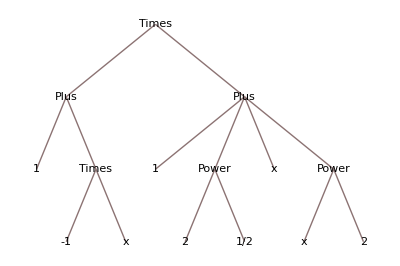

```mathematica
TreeForm[a]
```

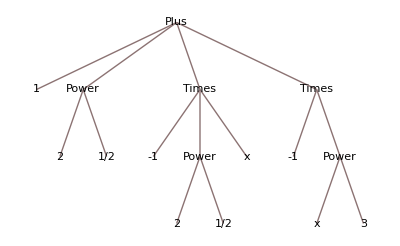

```mathematica
TreeForm[b]
```

```mathematica
FullForm[b]
```

Plus[1,Power[2,Rational[1,2]],Times[-1,Power[x,3]]]

```mathematica
b =Apply[List,b]
```

{1,√2,-x^3}

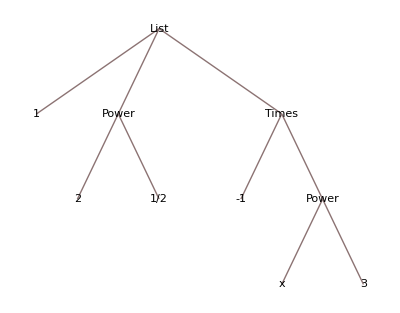

```mathematica
TreeForm[b]
```

```mathematica
b=Apply[Times,b]
```

-√2 x^3

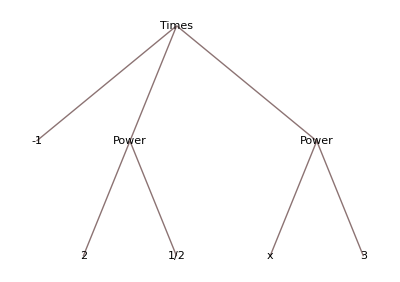

```mathematica
TreeForm[b]
```

## Drugi del

## Naloga 1

```mathematica
Clear[f,s,a,n,d]
```

```mathematica
Manipulate[Plot[a*x^2+b*x+c,{x,-10,10}],{a,-10,10},{b,-10,10},{c,-10,10}]
```

```mathematica
Manipulate[Plot[a Sin[b*x+c],{x,-10,10}],{a,-3,3},{b,-3,3},{c,-3,3}]
```

```mathematica
Manipulate[Plot[Sin[a*x]+Sin[b*x],{x,-10,10}],{a,1,20},{b,1,20}]
```

## Naloga 2

```mathematica
Manipulate[ExpandAll[(x-y)^n],{n,1,20,1}]
```

```mathematica
Manipulate[TrigExpand[Sin[n*x]],{n,1,20,1}]
```

```mathematica
Manipulate[x^2,{x,1,n,1},{n,1,20,1}]
```

```mathematica
Manipulate[Sin[x*Pi/2],{x,1,n,1},{n,1,20,1}]
```

## Met žoge

```mathematica
v0={10,3}
```

{10,3}

```mathematica
H=10
```

10

```mathematica
V[t_]:=X/t
```

```mathematica
X[t_]:=V*t
```

```mathematica
Manipulate[Plot[V[t],Axes->True,PlotRange->{{-1,25},{-5,15}},AspectRatio->Automatic],{t,0,5}]
```